```mathematica
SetDirectory[NotebookDirectory[]];
Get[FileNameJoin[{Directory[],"HexaBoxModules.m"}]];
PureIntegralsDB=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisDB1.txt"}]];
PureIntegralsPTB=ReadList[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisPtb1.txt"}]];
```

hxb[1,0,0,1,0,0,1,0,0,0,0,0,0]

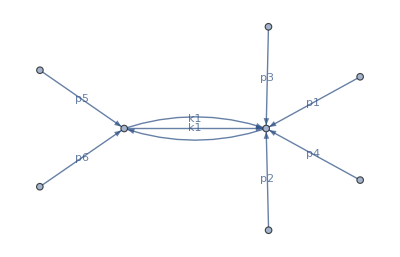

```mathematica
Ints=Cases[PureIntegralsPTB[[68]],_hxb,Infinity];
Sectors=Ints/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) //DeleteDuplicates;
TopSector=Total[Sectors/.hxb->List,{1}]/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) /.List->hxb
plotDiagram[TopSector]
```

hxb[1,0,0,1,1,0,0,0,0,0,0,0,0]

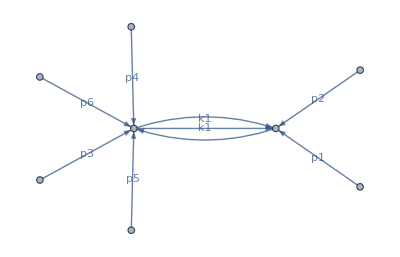

```mathematica
Ints=Cases[PureIntegralsDB[[2]],_hxb,Infinity];
Sectors=Ints/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) //DeleteDuplicates;
TopSector=Total[Sectors/.hxb->List,{1}]/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) /.List->hxb
plotDiagram[TopSector]
```

```mathematica
SectorsL=LaportaBasis/.( n_Integer:>0/;n<0)/.( n_Integer:>1/;n>1) //DeleteDuplicates;
Position[SectorsL,hxb[1,0,0,1,0,0,1,0,0,0,0,0,0]]
```

{{52}}

# Compute U matrix for Double Ints

```mathematica
$P=2^31-1;
tPoint=GetRandomPT[0,$P]
DeleteOldKiraRun[]
WriteNumericsFile[tPoint]
epsrepl={(ep->(4-d)/2)/.tPoint};
PureIntegrals=Join[Reverse[PureIntegralsPTB],PureIntegralsDB];
PureIntegralN=Expand[PureIntegrals/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;

ToReduce2=Cases[PureIntegralN,_hxb,Infinity]//DeleteDuplicates//EchoFunction[Length];
Export[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}],ToReduce2];
GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];

GenerateSectorsFromReductionList[FileNameJoin[{NotebookDirectory[],"KIRA/ExtraRelationsReduList.txt"}]];
WriteJobFile[{"ExtraRelationsReduList","UReduList"}]
```

{d→871090632,mt2→1368438556,s12→1254562352,s123→238926875,s16→860104470,s23→1501372711,s234→249189559,s34→71975735,s345→606144650,s45→37371688,s56→1385497943}

0.20356

588

```mathematica
reductionRules=GetReductionTableFromFile[FileNameJoin[{NotebookDirectory[],"KIRA/results/hxb/numerics_2147483647_0.m"}]];
Ureduce=ReadList[FileNameJoin[{NotebookDirectory[],"KIRA/UReduList.txt"}]];
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralN2=Expand[PureIntegralN/.reductionRules,Modulus->$P];
PureIntegralN3=Expand[PureIntegralN2/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralN4=Expand[PureIntegralN3/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates//Length
SubLaporta=Cases[PureIntegralN4,_hxb,Infinity]//DeleteDuplicates;
```

102

```mathematica
SubLaporta//Length
```

102

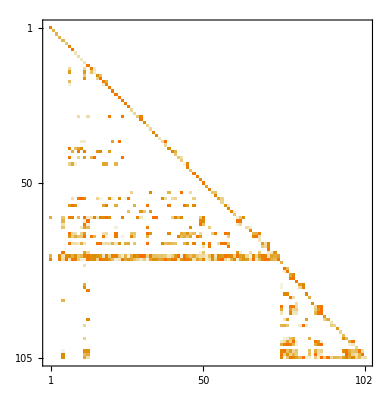

```mathematica
BasisChangMat=Table[CoefficientArrays[PureIntegralN4[[pos]],SubLaporta],{pos,1,Length[PureIntegralN4]}];
BasisChangMat=Normal[BasisChangMat[[All,2]]];
BasisChangMat//MatrixPlot
BasisChangMat/.(n_Integer/;n>0):>1//MatrixForm;
```

```mathematica
SubLaporta[[5]]
SubLaporta[[12]]
SubLaporta[[13]]
```

hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]

hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]

hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]

```mathematica
PureIntegralNDB=Expand[PureIntegralsDB/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralNDB=Expand[PureIntegralNDB/.reductionRules,Modulus->$P];
PureIntegralNDB=Expand[PureIntegralNDB/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralNDB=Expand[PureIntegralNDB/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
```

0.000824

```mathematica
Position[PureIntegralNDB,SubLaporta[[5]]]
Position[PureIntegralNDB,SubLaporta[[12]]]
Position[PureIntegralNDB,SubLaporta[[13]]]
```

{{13,2},{29,13,2},{30,13,2},{31,18,2}}

{{2,2},{8,1,2},{9,1,2},{21,2,2},{25,4,2},{29,4,2},{30,4,2},{31,5,2}}

{{10,2},{19,4,2},{29,8,2},{30,8,2},{31,9,2}}

```mathematica
PureIntegralsNPTB=Expand[Reverse[PureIntegralsPTB]/.tPoint/.epsrepl/.root[n_]:>PowerMod[n,1/2,$P],Modulus->$P]//EchoTiming;
ExtraRelations=GetExtraRelationReplacements[reductionRules,tPoint];
PureIntegralsNPTB=Expand[PureIntegralsNPTB/.reductionRules,Modulus->$P];
PureIntegralsNPTB=Expand[PureIntegralsNPTB/.ExtraRelations,Modulus->$P];

NonZeros=Cases[reductionRules,_hxb,Infinity]//DeleteDuplicates;
ZeroInts=Complement[Ureduce,NonZeros];
ZeroIntsRepl=Thread[Rule[ZeroInts,0]];
PureIntegralsNPTB=Expand[PureIntegralsNPTB/.ExtraRelations/.ZeroIntsRepl,Modulus->$P];
```

0.20665

```mathematica
Position[PureIntegralsNPTB,SubLaporta[[5]]]
Position[PureIntegralsNPTB,SubLaporta[[12]]]
Position[PureIntegralsNPTB,SubLaporta[[13]]]
```

{{5,2},{61,16,2},{62,3,2},{63,3,2},{64,4,2},{72,3,2},{73,33,2},{74,33,2}}

{{12,2},{14,1,2},{15,1,2},{16,2,2},{17,2,2},{37,2,2},{40,3,2},{42,1,2},{55,5,2},{61,4,2},{62,1,2},{63,1,2},{64,1,2},{66,1,2},{67,1,2},{69,5,2},{72,1,2},{73,7,2},{74,7,2}}

{{13,2},{29,4,2},{61,9,2},{62,2,2},{63,2,2},{64,3,2},{72,2,2},{73,17,2},{74,17,2}}

# DB13 = PTB5 (reversed)

```mathematica
PureIntegralsDB[[13]]//Factor
Reverse[PureIntegralsPTB][[5]]//Factor
```

ep^2 (-1+2 ep)^2 hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]

ep^2 (-1+2 ep)^2 hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]

# DB2 = PTB12 (reversed)

```mathematica
PureIntegralsDB[[2]]//Factor
Reverse[PureIntegralsPTB][[12]]//Factor
```

-(ep (-1+2 ep) (-2+3 ep) (-1+3 ep) hxb[1,0,0,1,1,0,0,0,0,0,0,0,0])/s12

-(ep (-1+2 ep) (-2+3 ep) (-1+3 ep) hxb[0,0,1,1,0,0,0,0,1,0,0,0,0])/s12

# DB10 = PTB13 (reversed)

```mathematica
PureIntegralsDB[[10]]//Factor
Reverse[PureIntegralsPTB][[13]]//Factor
```

ep^2 (-1+2 ep) (-1+3 ep) hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]

ep^2 (-1+2 ep) (-1+3 ep) hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]

Part::pspec1: Part specification NotFound is not applicable.

First::normal: Nonatomic expression expected at position 1 in First[NonzeroPositions].

Part::pspec1: Part specification NotFound is not applicable.

First::normal: Nonatomic expression expected at position 1 in First[NonzeroPositions].

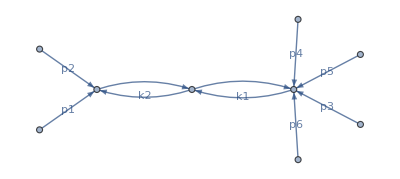

-Graphics-

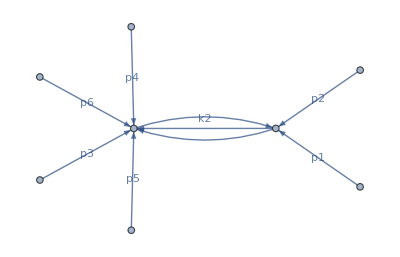

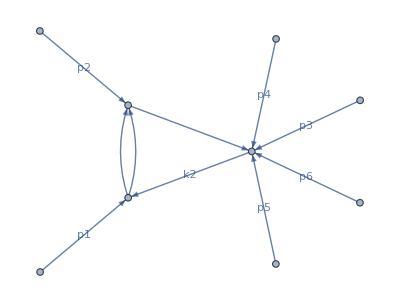

```mathematica
plotDiagram[hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]]
plotDiagram[hxb[1,0,0,1,1,0,0,0,0,0,0,0,0]]
plotDiagram[ hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]]
plotDiagram[ hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]]
```

```mathematica
hxb[1,0,0,1,1,0,0,0,0,0,0,0,0]/.reductionRules
hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]/.reductionRules
```

hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]

hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]

```mathematica
PureIntegralN4[[12]]
PureIntegralN4[[2+74]]
```

310807801 hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]

310807801 hxb[0,0,1,1,0,0,0,0,1,0,0,0,0]

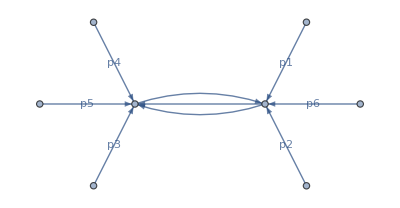

```mathematica
plotDiagram[SubLaporta[[79]]]
```

```mathematica
PureIntegrals[[{5,13+74}]]//Factor
PureIntegrals[[{12,2+74}]]//Factor
PureIntegrals[[{13,10+74}]]//Factor
PureIntegrals2=Delete[PureIntegrals,{{13+74},{2+74},{10+74}}]
```

{ep^2 (-1+2 ep)^2 hxb[1,0,1,0,1,0,0,0,1,0,0,0,0],ep^2 (-1+2 ep)^2 hxb[1,0,1,0,1,0,0,0,1,0,0,0,0]}

{-(ep (-1+2 ep) (-2+3 ep) (-1+3 ep) hxb[0,0,1,1,0,0,0,0,1,0,0,0,0])/s12,-(ep (-1+2 ep) (-2+3 ep) (-1+3 ep) hxb[1,0,0,1,1,0,0,0,0,0,0,0,0])/s12}

{ep^2 (-1+2 ep) (-1+3 ep) hxb[0,1,0,1,1,0,0,0,1,0,0,0,0],ep^2 (-1+2 ep) (-1+3 ep) hxb[0,1,0,1,1,0,0,0,1,0,0,0,0]}

```mathematica
PureIntegrals2;
PureIntegralsPTB=Export[FileNameJoin[{NotebookDirectory[],"files/PureIntegralBasisP1.txt"}],PureIntegrals2]
```

/home/dschiebe/Documents/lanayru/PhD_Files/PureInts_ttH/HexaBox2/files/PureIntegralBasisP1.txt